# Brute-force classify

MSTに対して、CVI評価と最長エッジの削除を繰り返し、クラスタ数が1からNまでのCVIを得て、最良のCVIを持つクラシフィケーションを選択する。

必要なデータ: 
- 距離行列 (V * V)
- MST (2 * E)
- 連結行列(ノード同士が何ステップでつながっているか) (V * V)
- クラス分けリスト (V * V)

CVI:
CNS3 (mstPi2rkS[3] @ Cluster+Distance_Operations.txt)
CNS4 (mstPi2rkS[4] @ Cluster+Distance_Operations.txt)

## 準備

```mathematica
$CharacterEncoding="UTF-8"
```

UTF-8

```mathematica
SetDirectory["/Users/kouamano/gitsrc/Brute-force-classify"]
```

SetDirectory::cdir: Cannot set current directory to "/Users/kouamano/gitsrc/Brute-force-classify".

$Failed

## 手順Example

データ:

```mathematica
data1={{0.7598461064538076,0.2762446676639849},{0.052506257778350385,0.4754933397861183},{0.835725205441473,0.971833104200341},{0.6256858201023905,0.39269853076870276},{0.8735494574667926,0.12663983198252038},{0.7508780147998599,0.6241170701623782},{0.2698064552281392,0.7247970742521272}}
```

{{0.759846,0.276245},{0.0525063,0.475493},{0.835725,0.971833},{0.625686,0.392699},{0.873549,0.12664},{0.750878,0.624117},{0.269806,0.724797}}

```mathematica
(*data1=Table[{RandomReal[],RandomReal[]},{7}]*)
```

距離行列:

```mathematica
(data1dmat=Outer[EuclideanDistance,data1,data1,1])//MatrixForm
```

(0. | 0.734867 | 0.699715 | 0.177653 | 0.18791 | 0.347988 | 0.664333
0.734867 | 0. | 0.927246 | 0.579128 | 0.892082 | 0.714011 | 0.330714
0.699715 | 0.927246 | 0. | 0.616047 | 0.846039 | 0.357918 | 0.617488
0.177653 | 0.579128 | 0.616047 | 0. | 0.363626 | 0.263111 | 0.486764
0.18791 | 0.892082 | 0.846039 | 0.363626 | 0. | 0.512379 | 0.849881
0.347988 | 0.714011 | 0.357918 | 0.263111 | 0.512379 | 0. | 0.491494
0.664333 | 0.330714 | 0.617488 | 0.486764 | 0.849881 | 0.491494 | 0.)

距離行列書き出し:

```mathematica
Export["data1.dmat",data1dmat,"TSV"]
```

data1.dmat

MST:

```mathematica
Run["/usr/local/bin/MST dmat=data1.dmat > data1.mst"]
```

0

MSTの読み込み:

```mathematica
(mst=Map[#+{1,1,0}&,Import["data1.mst","TSV"]])//TableForm
```

1 | 4 | 0.177653
1 | 5 | 0.18791
4 | 6 | 0.263111
6 | 3 | 0.357918
4 | 7 | 0.486764
7 | 2 | 0.330714

Plot:

:edge:

```mathematica
pos=Map[#[[{1,2}]]&,mst]
```

{{1,4},{1,5},{4,6},{6,3},{4,7},{7,2}}

:line coordinate:

```mathematica
cod=Map[data1[[#]]&,pos,{2}]
```

{{{0.759846,0.276245},{0.625686,0.392699}},{{0.759846,0.276245},{0.873549,0.12664}},{{0.625686,0.392699},{0.750878,0.624117}},{{0.750878,0.624117},{0.835725,0.971833}},{{0.625686,0.392699},{0.269806,0.724797}},{{0.269806,0.724797},{0.0525063,0.475493}}}

```mathematica
line=Map[Line[#]&,cod,{1}]
```

{Line[{{0.759846,0.276245},{0.625686,0.392699}}],Line[{{0.759846,0.276245},{0.873549,0.12664}}],Line[{{0.625686,0.392699},{0.750878,0.624117}}],Line[{{0.750878,0.624117},{0.835725,0.971833}}],Line[{{0.625686,0.392699},{0.269806,0.724797}}],Line[{{0.269806,0.724797},{0.0525063,0.475493}}]}

:Plot:

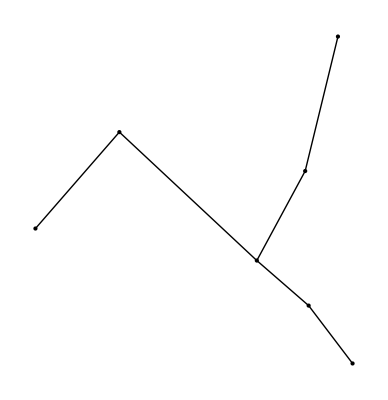

```mathematica
Graphics[{Map[Point,data1],line}]
```

連結行列 (MSTの情報より連結可能なパスが唯一のバスなので連結可能なパスを調べれば良い):

```mathematica
(conj={
{0,3,3,1,1,2,2},
{3,0,4,2,4,3,1},
{3,4,0,2,4,1,3},
{1,2,2,0,2,1,1},
{1,4,4,2,0,3,3},
{2,3,1,1,3,0,2},
{2,1,3,1,3,2,0}})//MatrixForm
```

(0 | 3 | 3 | 1 | 1 | 2 | 2
3 | 0 | 4 | 2 | 4 | 3 | 1
3 | 4 | 0 | 2 | 4 | 1 | 3
1 | 2 | 2 | 0 | 2 | 1 | 1
1 | 4 | 4 | 2 | 0 | 3 | 3
2 | 3 | 1 | 1 | 3 | 0 | 2
2 | 1 | 3 | 1 | 3 | 2 | 0)

クラス分けリスト:

:最初:

```mathematica
{0,0,0,0,0,0,0}
```

{0,0,0,0,0,0,0}

:1回目、4-7で切断:

:グループの判定、ステップが近い方のグループに書き換える:

```mathematica
conj[[{4,7}]]//TableForm
```

1 | 2 | 2 | 0 | 2 | 1 | 1
2 | 1 | 3 | 1 | 3 | 2 | 0

```mathematica
{0,0,0,0,0,0,0} -> {4,7,4,4,4,4,7} (*2、7番目がgroup7*)
```

{0,0,0,0,0,0,0}→{4,7,4,4,4,4,7}

: プログラム :
/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]
```

```mathematica
conjMat=conjMatFromAdjE[pos]
```

{{0,3,3,1,1,2,2},{3,0,4,2,4,3,1},{3,4,0,2,4,1,3},{1,2,2,0,2,1,1},{1,4,4,2,0,3,3},{2,3,1,1,3,0,2},{2,1,3,1,3,2,0}}

```mathematica
conjMat==conj
```

True

CVI評価:

:CVIの入力形式に変換:

:CVI評価: